## RemoveCell-example.nb RemoveCell,RemoveEdge,RemoveVertex

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (10-Nov-2012)) loaded Sat 10 Nov 2012 16:29:04
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
w=TemplateHoneycombCover[5,5];
```

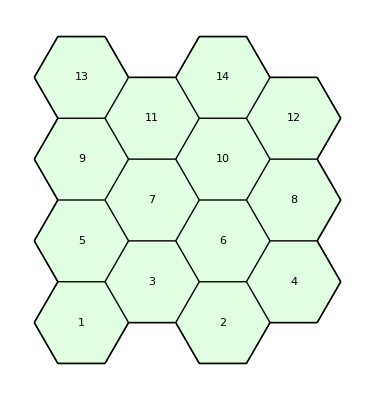

```mathematica
ShowTissue[w,"CellNumbers"-> True]
```

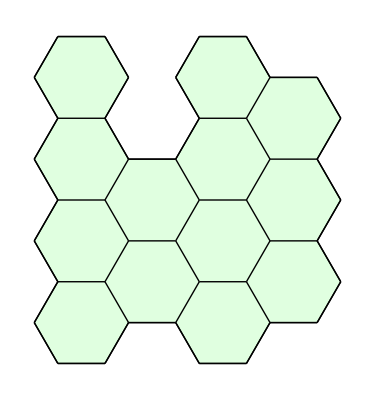

```mathematica
w1=RemoveCell[w, 11];
ShowTissue[w1]
```

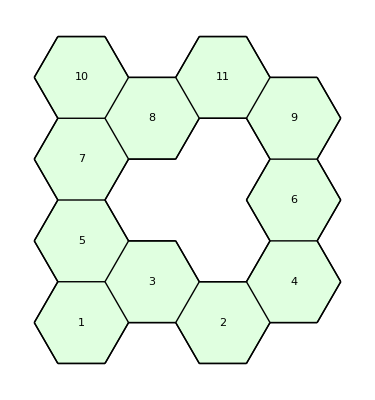

```mathematica
ShowTissue[RemoveCell[w,{6,7,10}],"CellNumbers"-> True]
```

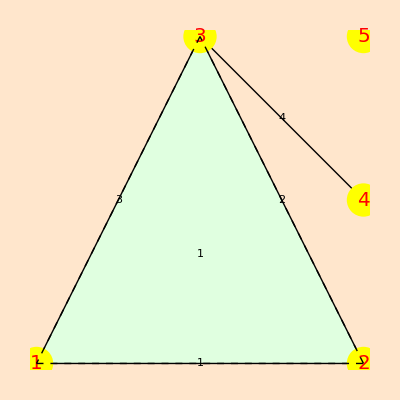

```mathematica
v={{0,0},{2,0},{1,2},{2,1},{2,2}};
e={{1,2},{2,3},{3,1},{3,4}};
c={{1,2,3}};
q=Tissue[v,e,c];
ShowTissue[q,"Vertices"->{Yellow,PointSize[.06]},"VertexNumbers"-> True, "VertexNumberStyle"->{Red,FontSize->20},"CellNumbers"->True,"EdgeNumbers"->True,"All"->True,"BoundaryStyle"->Dashed,Background->LightOrange]
```

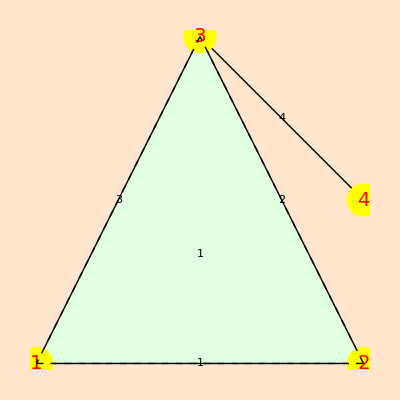

```mathematica
ShowTissue[RemoveVertex[q,5],"Vertices"->{Yellow,PointSize[.06]},"VertexNumbers"->True, "VertexNumberStyle"-> {Red,FontSize->20},"CellNumbers"->True,"EdgeNumbers"->True,"All"->True,"BoundaryStyle"->Dashed,Background->LightOrange]
```

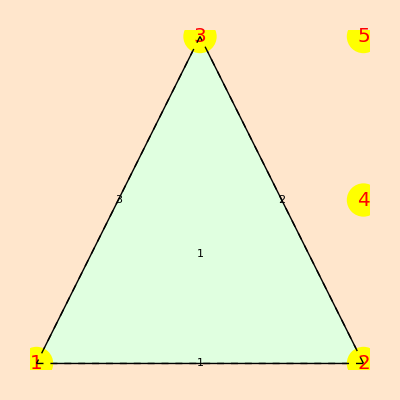

```mathematica
ShowTissue[RemoveEdge[q,4],"Vertices"->{Yellow,PointSize[.06]},"VertexNumbers"->True, "VertexNumberStyle"-> {Red,FontSize->20},"CellNumbers"->True,"EdgeNumbers"->True,"All"->True,"BoundaryStyle"->Dashed,Background->LightOrange]
```